#### Black-Scholes Process

```mathematica
r=0.4;
xStrike=500;
T=30;
σ=0.2;
x0=600;
```

```mathematica
stoh[t_,r_,σ_]:=x0 ⅇ^((r-σ^2/2)t+σ √t RandomVariate[NormalDistribution[0,1]])
```

```mathematica
blackScholes[t_,σ_,xStrike_,r_,T_]:=Module[{s=stoh[t,r,σ]},s *CDF[NormalDistribution[0,1],(Log[s/xStrike]+(r+σ^2/2)(T-t))/(σ √(T-t))]-xStrike* ⅇ^(-r(T-t))*CDF[NormalDistribution[0,1],(Log[s/xStrike]+(r-σ^2/2)(T-t))/(σ √(T-t))]]
```

#### Visualization

```mathematica
Framed[Manipulate[ListLinePlot[Table[Table[If[σ!=0,blackScholes[t,σ,xStrike,r,T],blackScholes[t,0.001,xStrike,r,T]],{t,1,T-1}],5]],{{r,0.04},0,0.1},{{σ,0.2},0,2,0.01},{{T,30},2,100,1},ControlPlacement->Left,Paneled->False],RoundingRadius->5]
```

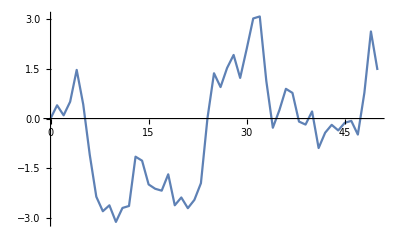

```mathematica
ListLinePlot[RandomFunction[WienerProcess[0,1],{0,50,1}]]
```